```mathematica
Clear["Global`*"]
```

```mathematica
V[x_] :=   .25x^4
```

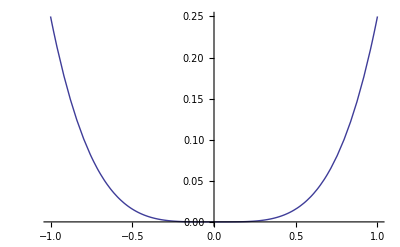

```mathematica
Plot[V[x], {x, -1, 1}]
```

```mathematica
L=4;
```

```mathematica
eqn[en_] := u''[x] + 2(en - V[x])u[x]
```

```mathematica
wavefunc[en_] := NDSolve[{ eqn[en] == 0, u[-L] ==  0, 
					u'[-L] == 1}, u, {x, -L, 0} ]
```

```mathematica
sol[x_?NumericQ, en_?NumericQ] := u[x] /.wavefunc[en][[1]]
```

```mathematica
solprime[x_?NumericQ, en_?NumericQ] := u'[x] /.wavefunc[en][[1]]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 0, .5} ]
```

0.420805

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn[x_] := efunc[x] /; x≤ 0 ;
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0 ;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

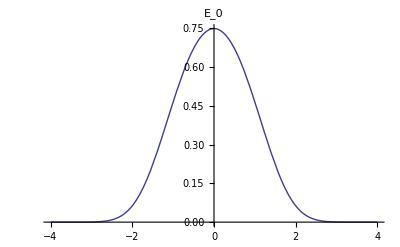

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_0"]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 1, 1.9} ]
```

2.9588

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn [x_] := -efunc[-x] /; x > 0
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

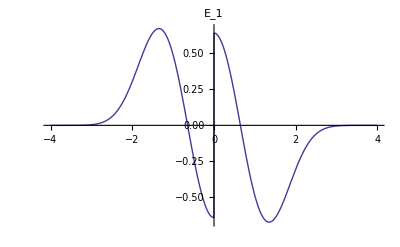

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_1"]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 1.3, 3.5} ]
```

2.9588

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn[x_] := efunc[x] /; x≤ 0 ;
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0 ;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

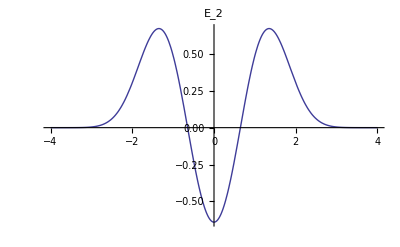

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_2"]
```